```mathematica
SetDirectory["c:\\git\\ElectronMonteCarlo\\test"]
```

c:\git\ElectronMonteCarlo\test

```mathematica
testSet3=Drop[Import["dataSet3","table"],2];
```

```mathematica
testSet4=Drop[Import["dataSet4","table"],2];
```

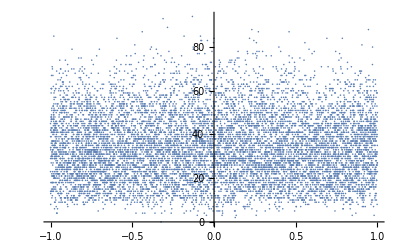

```mathematica
ListPlot[testSet3]
```

```mathematica
BinPlot[data_,nBins_]:=Module[{bins,counts,sums,squareSums,means,stdevs,binCenters,plotdata},
bins={-1,1,2/nBins};
counts=HistogramList[data[[All,1]],bins][[2]];
counts=counts+Reverse[counts];
sums=HistogramList[WeightedData[data[[All,1]],data[[All,2]]],bins][[2]];
sums=sums+Reverse[sums];
squareSums=HistogramList[WeightedData[data[[All,1]],data[[All,2]]^2],bins][[2]];
squareSums= squareSums+Reverse[squareSums];
means=sums/counts;
stdevs=Sqrt[squareSums/counts-means^2]/Sqrt[counts];
binCenters=2/nBins(Range[nBins]-1/2)-1;
plotdata=Transpose[{binCenters,Around[#[[1]],#[[2]]]&/@Transpose[{means,stdevs}]}];
ListPlot[plotdata,PlotRange->{{-1,1},{0,All}},IntervalMarkers->"Bars",PlotStyle->Red,PlotMarkers->"OpenMarkers"]
]
```

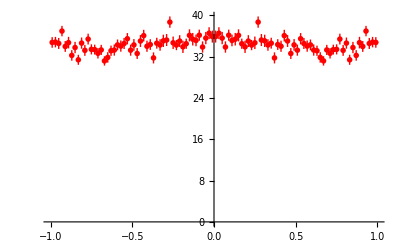

```mathematica
bp=BinPlot[testSet3,100]
```

```mathematica
lmf=LinearModelFit[testSet3,LegendreP[#,z]&/@{0,2,4,6,8,10},z,ConfidenceLevel->0.65]
```

FittedModel[34.3267-0.459562 (-1+3 z^2)+«19» «1»+«1»-0.00360723 («1»)-0.00188183 (-63+3465 z^2-30030 z^4+90090 z^6-109395 z^8+46189 z^10)]

```mathematica
lmf4=LinearModelFit[testSet4,LegendreP[#,z]&/@{0,2,4,6,8,10},z,ConfidenceLevel->0.65]
```

FittedModel[34.0388-0.371894 (-1+3 z^2)+«1»+«1»-0.00414438 («6»+«1»)-0.00106341 (-63+3465 z^2-30030 z^4+90090 z^6-109395 z^8+46189 z^10)]

```mathematica
lmf["ParameterConfidenceIntervals"]
```

{{34.1841,34.4692},{-1.23627,-0.601978},{1.67121,2.52522},{-0.32035,0.707621},{-1.05132,0.127864},{-1.13591,0.172411}}

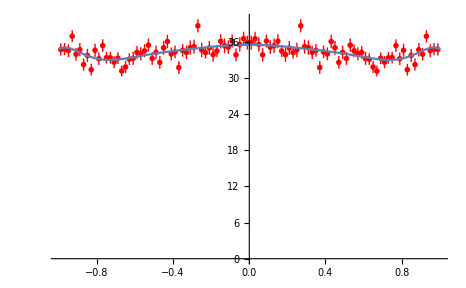

```mathematica
Show[BinPlot[testSet3,100],Plot[lmf[z],{z,-1,1}]]
```

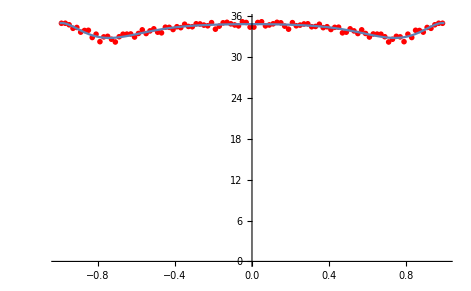

```mathematica
Show[BinPlot[testSet4,100],Plot[lmf4[z],{z,-1,1}]]
```

```mathematica
lmf["ParameterTable"]
```

General::munfl: Exp[-9013.5] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 34.3267 | 0.152544 | 225.028 | 0.
1/2 (-1+3 z^2) | -0.919124 | 0.339326 | -2.70867 | 0.00676676
1/8 (3-30 z^2+35 z^4) | 2.09822 | 0.456872 | 4.59257 | 4.43167×10^-6
1/16 (-5+105 z^2-315 z^4+231 z^6) | 0.193635 | 0.549933 | 0.352107 | 0.724765
1/128 (35-1260 z^2+6930 z^4-12012 z^6+6435 z^8) | -0.461726 | 0.630825 | -0.73194 | 0.464222
1/256 (-63+3465 z^2-30030 z^4+90090 z^6-109395 z^8+46189 z^10) | -0.48175 | 0.699912 | -0.6883 | 0.49128

```mathematica
lmf4["ParameterTable"]
```

General::munfl: Exp[-90354.4] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 34.0388 | 0.0476997 | 713.605 | 0.
1/2 (-1+3 z^2) | -0.743788 | 0.106491 | -6.98449 | 2.87677×10^-12
1/8 (3-30 z^2+35 z^4) | 1.80765 | 0.143173 | 12.6257 | 1.62582×10^-36
1/16 (-5+105 z^2-315 z^4+231 z^6) | 0.653254 | 0.171903 | 3.80013 | 0.000144703
1/128 (35-1260 z^2+6930 z^4-12012 z^6+6435 z^8) | -0.530481 | 0.196663 | -2.69741 | 0.0069892
1/256 (-63+3465 z^2-30030 z^4+90090 z^6-109395 z^8+46189 z^10) | -0.272232 | 0.218934 | -1.24344 | 0.213708

```mathematica
bands=lmf["MeanPredictionBands",ConfidenceLevel->.65]
```

{35.5049-9.95171 z^2+36.8809 z^4-123.409 z^6+182.651 z^8-86.92 z^10-0.934633 √(0.170988-7.41624 z^2+189.321 z^4-2176.89 z^6+13629.4 z^8-50858.9 z^10+118074. z^12-171984. z^14+152739. z^16-75550. z^18+15947.2 z^20),35.5049-9.95171 z^2+36.8809 z^4-123.409 z^6+182.651 z^8-86.92 z^10+0.934633 √(0.170988-7.41624 z^2+189.321 z^4-2176.89 z^6+13629.4 z^8-50858.9 z^10+118074. z^12-171984. z^14+152739. z^16-75550. z^18+15947.2 z^20)}

```mathematica
bands4=lmf4["MeanPredictionBands",ConfidenceLevel->.65]
```

{34.8063-2.07018 z^2-1.73894 z^4-36.5886 z^6+89.6622 z^8-49.1177 z^10-0.934594 √(0.0165387-0.717756 z^2+18.3471 z^4-211.302 z^6+1325.07 z^8-4952.32 z^10+11514.1 z^12-16792.4 z^14+14928.2 z^16-7389.17 z^18+1560.36 z^20),34.8063-2.07018 z^2-1.73894 z^4-36.5886 z^6+89.6622 z^8-49.1177 z^10+0.934594 √(0.0165387-0.717756 z^2+18.3471 z^4-211.302 z^6+1325.07 z^8-4952.32 z^10+11514.1 z^12-16792.4 z^14+14928.2 z^16-7389.17 z^18+1560.36 z^20)}

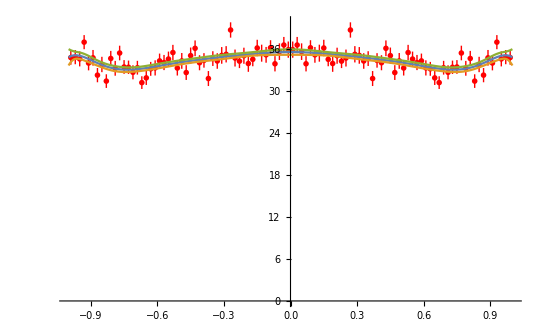

```mathematica
Show[BinPlot[testSet3,100],Plot[{lmf[z],bands[[1]],bands[[2]]},{z,-1,1}]]
```

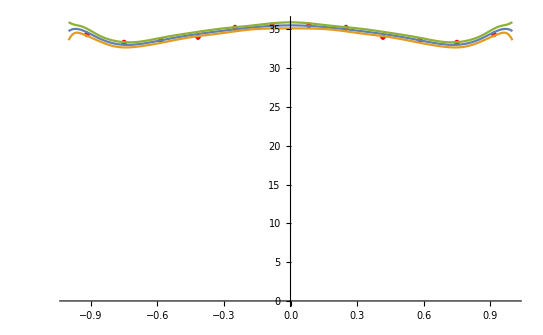

```mathematica
Show[BinPlot[testSet3,12],Plot[{lmf[z],bands[[1]],bands[[2]]},{z,-1,1}]]
```

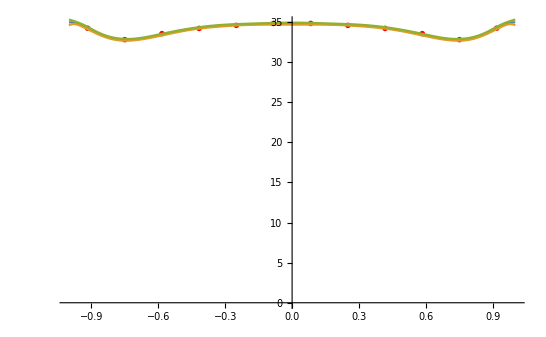

```mathematica
Show[BinPlot[testSet4,12],Plot[{lmf4[z],bands4[[1]],bands4[[2]]},{z,-1,1}]]
```

```mathematica
With[{zz=0},ions=lmf[zz];Around[ions,{ions-bands[[1]],bands[[2]]-ions}]/.z->zz]
```

35.50.40.4

```mathematica
With[{zz=0.95},ions=lmf[zz];Around[ions,{ions-bands[[1]],bands[[2]]-ions}]/.z->zz]
```

35.00.50.5

```mathematica
bands4=lmf4["MeanPredictionBands",ConfidenceLevel->.65];
```

```mathematica
With[{zz=0},ions=lmf4[zz];Around[ions,ions-bands4[[1]]]/.z->zz]
```

34.810.12

```mathematica
With[{zz=.95},ions=lmf4[zz];Around[ions,ions-bands4[[1]]]/.z->zz]
```

34.700.15

```mathematica
With[{zz=1.0},ions=lmf4[zz];Around[ions,ions-bands4[[1]]]/.z->zz]
```

35.00.4

```mathematica
With[{zz=0.99},ions=lmf4[zz];Around[ions,ions-bands4[[1]]]/.z->zz]
```

34.970.26

```mathematica
With[{zz=0.98},ions=lmf4[zz];Around[ions,ions-bands4[[1]]]/.z->zz]
```

34.950.20

```mathematica
With[{zz=0.90},ions=lmf4[zz];Around[ions,ions-bands4[[1]]]/.z->zz]
```

34.010.13

```mathematica
{lmf[z],bands[[1]],bands[[2]]}/.z->0
```

{35.5049,35.1184,35.8913}

```mathematica
{lmf[z],bands[[1]],bands[[2]]}/.z->0.98
```

{35.0167,34.386,35.6474}

```mathematica
{lmf[z],bands[[1]],bands[[2]]}/.z->0.96
```

{35.0339,34.5627,35.505}

```mathematica
{lmf[z],bands[[1]],bands[[2]]}/.z->0.94
```

{34.892,34.425,35.359}